```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/mathematica/David/surf"];
fileSurfs={"surf_1_P_T_G.dat"};
cacSurf=Table[ReadList[fileSurfs[[i]],{Number, Number,Number}],{i,1,Length[fileSurfs]}];
```

```mathematica
cacSurf[[1]][[-1]]
```

{10.8555,2000.,-941.479}

```mathematica
ListPlot3D[cacSurf[[1]]]
```

-Graphics3D-

```mathematica
eqnForm=aaa+bbb*T+ccc*p+ddd*T^2+eee*p^2+fff*p*T;
```

```mathematica
fittedSurf=NonlinearModelFit[cacSurf[[1]],eqnForm,{aaa,bbb,ccc,ddd,eee,fff},{p,T}]
```

FittedModel[-941.488+0.0146882 p-0.0000964396 p^2-0.0000253548 T+3.77171×10^-7 p T-2.4741×10^-8 T^2]

```mathematica
fittedSurf
```

FittedModel[-941.488+0.0146882 p-0.0000964396 p^2-0.0000253548 T+3.77171×10^-7 p T-2.4741×10^-8 T^2]

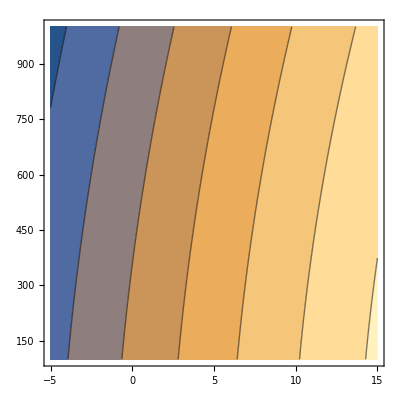

```mathematica
ContourPlot[fittedSurf[p,T],{p,-5,15},{T,100,1000}]
```

```mathematica
p1=Plot3D[fittedSurf[p,T],{p,-4,12},{T,100,2000}]
p2=ListPlot3D[cacSurf[[1]]]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[ListPlot3D[cacSurf[[1]],PlotStyle->Red],Plot3D[fittedSurf[p,T],{p,-4,12},{T,100,2000}]]
```

-Graphics3D-

```mathematica
fittedSurf
```

FittedModel[-941.488+0.0146882 p-0.0000964396 p^2-0.0000253548 T+3.77171×10^-7 p T-2.4741×10^-8 T^2]

```mathematica
fittedSurf[5,1000]
```

-941.465

```mathematica
Show[p1,p2]
```

-Graphics3D-

```mathematica
Show[Plot3D[fittedSurf[p,T]+20,{p,-5,15},{T,100,1000}],ListPlot3D[cacSurf[[1]]]]
```

-Graphics3D-